```mathematica
f=(-x-y+11)^2+(x (-y)+x+10 y+1)^2
Minimize[f,{x,y}]
FindMinimum[{f,0.24 x+y-6==0,(x-20)^2+(y-1)^2≤4},{x,y}]
```

(-x-y+11)^2+(x (-y)+x+10 y+1)^2

{40,{x→7,y→-2}}

{109.278,{x→18.1098,y→1.65364}}

NMinimize::incst:NMinimize was unable to generate any initial points satisfying the inequality constraints {-4 + (5.`  - 0.24` x)^2 + (-20 + x)^2 ≤ 0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

{109.278,{x→18.1098,y→1.65364}}

```mathematica
Null
```

{109.278,{x→18.1098,y→1.65364}}

```mathematica
FindMinimum[{f,0.24 x+y-6==0,(x-20)^2+(y-1)^2≤4},{x,y}]
```

{109.278,{x→18.1098,y→1.65364}}

```mathematica
α=tan^-1((a+b)/x)-tan^-1(a/x)
```

tan^-1((a+b)/x)-tan^-1(a/x)

```mathematica
(∂α)/(∂x)
Simplify[%]
sol=Simplify[Solve[%==0,x]]
xsol=x/.sol⟦2⟧
(∂^2 α)/(∂x^2)
%/.x->xsol
Simplify[%]
```

a/(x^2 (a^2/x^2+1))-(a+b)/(x^2 ((a+b)^2/x^2+1))

(b (a^2+a b-x^2))/((a^2+x^2) (a^2+2 a b+b^2+x^2))

{{x→-√(a (a+b))},{x→√(a (a+b))}}

√(a (a+b))

-(2 a)/(x^3 (a^2/x^2+1))+(2 a^3)/(x^5 (a^2/x^2+1)^2)-(2 (a+b)^3)/(x^5 ((a+b)^2/x^2+1)^2)+(2 (a+b))/(x^3 ((a+b)^2/x^2+1))

(2 a^3)/((a (a+b))^(5/2) (a/(a+b)+1)^2)-(2 a)/((a (a+b))^(3/2) (a/(a+b)+1))+(2 (a+b))/((a (a+b))^(3/2) ((a+b)/a+1))-(2 (a+b)^3)/((a (a+b))^(5/2) ((a+b)/a+1)^2)

-(2 b)/(√(a (a+b)) (2 a+b)^2)

(-x-y+11)^2+(x (-y)+x+10 y+1)^2

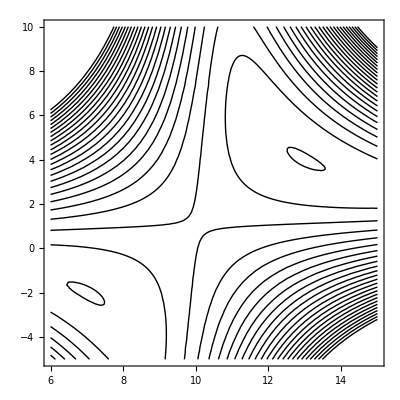

ContourPlot[f,{x,x_min,x_max},{y,y_min,y_max}] generates a contour plot of f as a function of x and y. 
ContourPlot[f==g,{x,x_min,x_max},{y,y_min,y_max}] plots contour lines for which f=g. 
ContourPlot[{f_1==g_1,f_2==g_2,…},{x,x_min,x_max},{y,y_min,y_max}] plots several contour lines.

```mathematica
f=(-x-y+11)^2+(x (-y)+x+10 y+1)^2
ContourPlot[f,{x,6,15},{y,-5,10},Contours->25,ContourStyle->Black,ContourShading->None]
Information["ContourPlot",LongForm->False]
```

```mathematica
Simplify[(∂f)/(∂x)]
Simplify[(∂f)/(∂y)]
solf=Solve[{(∂f)/(∂x)==0,(∂f)/(∂y)==0},{x,y}]
h11=Simplify[(∂^2 f)/(∂x^2)]
h22=Simplify[(∂^2 f)/(∂y^2)]
h12=h21=Simplify[(∂^2 f)/(∂x ∂y)]
```

2 x (y^2-2 y+2)-20 (y^2-y+1)

2 x^2 (y-1)+x (20-40 y)+202 y-2

{{x→7,y→-2},{x→10,y→1},{x→13,y→4},{x→10-ⅈ √11,y→1+ⅈ √11},{x→10+ⅈ √11,y→1-ⅈ √11}}

2 (y^2-2 y+2)

2 (x-10)^2+2

4 (x (y-1)-10 y+5)

```mathematica
solfx={{x->7,y->-2},{x->10,y->1},{x->13,y->4}}
H=({{2 (y^2-2 y+2), 4 (x (y-1)-10 y+5)}, {4 (x (y-1)-10 y+5), 2 (x-10)^2+2}})
eigs=Expand[Eigenvalues[H]]
eigs/.{x->7,y->-2}
eigs/.{x->10,y->1}
eigs/.{x->12,y->4}
f/.{x->7,y->-2}
f/.{x->10,y->1}
f/.{x->12,y->4}
```

{{x→7,y→-2},{x→10,y→1},{x→13,y→4}}

(2 (y^2-2 y+2) | 4 (x (y-1)-10 y+5)
4 (x (y-1)-10 y+5) | 2 (x-10)^2+2)

{x^2-√(x^4-40 x^3+14 x^2 y^2-28 x^2 y+614 x^2-280 x y^2+400 x y-4120 x+y^4-4 y^3+1406 y^2-1204 y+10201)-20 x+y^2-2 y+103,x^2+√(x^4-40 x^3+14 x^2 y^2-28 x^2 y+614 x^2-280 x y^2+400 x y-4120 x+y^4-4 y^3+1406 y^2-1204 y+10201)-20 x+y^2-2 y+103}

{4,36}

{-18,22}

{15-√41,15+√41}

40

121

50

```mathematica
"Kisitli optimizason"
Subscript[f, 1]=0.24 x+y-6
Subscript[g, 1]=(x-20)^2+(y-1)^2
Subscript[b, 1]=4
Subscript[f, L]=Subscript[f, 1] λ+f+Subscript[g, 1] μ
eqs={(∂Subscript[f, L])/(∂x)==0,(∂Subscript[f, L])/(∂y)==0,Subscript[f, 1]==0,μ (Subscript[g, 1]-Subscript[b, 1])==0}
Subscript[g, 1]≤Subscript[b, 1]
μ≥0
eq1={(∂Subscript[f, L])/(∂x)==0,(∂Subscript[f, L])/(∂y)==0,Subscript[f, 1]==0}/.μ->0
sol1=Solve[eq1,{x,y,λ}]
f/.{λ->23.572,x->13.6241,y->2.73021}
Subscript[g, 1]/.{λ->23.572,x->13.6241,y->2.73021}
sol2=Solve[eqs,{x,y,λ,μ}]
xt=x/.sol2[[5]]
yt=y/.sol2[[5]]
f/.{x->xt,y->yt}
N[Subscript[g, 1]/.{x->xt,y->yt}]
```

Kisitli optimizason

-6+0.24 x+y

(-20+x)^2+(-1+y)^2

4

(11-x-y)^2+(1+x+10 y-x y)^2+(-6+0.24 x+y) λ+((-20+x)^2+(-1+y)^2) μ

{-2 (11-x-y)+2 (1-y) (1+x+10 y-x y)+0.24 λ+2 (-20+x) μ==0,-2 (11-x-y)+2 (10-x) (1+x+10 y-x y)+λ+2 (-1+y) μ==0,-6+0.24 x+y==0,(-4+(-20+x)^2+(-1+y)^2) μ==0}

(-20+x)^2+(-1+y)^2≤4

μ≥0

{-2 (11-x-y)+2 (1-y) (1+x+10 y-x y)+0.24 λ==0,-2 (11-x-y)+2 (10-x) (1+x+10 y-x y)+λ==0,-6+0.24 x+y==0}

{{λ→-55.4353-3.5891 ⅈ,x→16.3129-4.89048 ⅈ,y→2.0849+1.17372 ⅈ},{λ→-55.4353+3.5891 ⅈ,x→16.3129+4.89048 ⅈ,y→2.0849-1.17372 ⅈ},{λ→23.572,x→13.6241,y→2.73021}}

51.0372

43.6457

{{λ→-55.4353-3.5891 ⅈ,μ→0.,x→16.3129-4.89048 ⅈ,y→2.0849+1.17372 ⅈ},{λ→-55.4353+3.5891 ⅈ,μ→0.,x→16.3129+4.89048 ⅈ,y→2.0849-1.17372 ⅈ},{λ→23.572,μ→0.,x→13.6241,y→2.73021},{λ→65.9519,μ→6.85257,x→18.1098,y→1.65364},{λ→304.722,μ→-26.3565,x→21.9809,y→0.724573}}

21.9809

0.724573

341.505

4.

```mathematica
P->min &   Subscript[g, 1]≥Subscript[b, 1] 
| Subscript[g, 1]->-Subscript[g, 1], Subscript[b, 1]->-Subscript[b, 1]|                             D[Subscript[f, 0],Subscript[x, i]]+Subscript[μ, 1] D[Subscript[g, 1],Subscript[x, i]]=0 ,Subscript[μ, 1](Subscript[b, 1]-Subscript[g, 1])=0 , ,Subscript[μ, 1]≥0

P->max &   Subscript[g, 1]≤Subscript[b, 1] 
| Subscript[f, 0]->-Subscript[f, 0]|                                              - D[Subscript[f, 0],Subscript[x, i]]+Subscript[μ, 1] D[Subscript[g, 1],Subscript[x, i]]=0 ,Subscript[μ, 1](Subscript[b, 1]-Subscript[g, 1])=0 , ,Subscript[μ, 1]≥0

P->max &   Subscript[g, 1]≥Subscript[b, 1] 
| Subscript[f, 0]->-Subscript[f, 0],Subscript[g, 1]->-Subscript[g, 1], Subscript[b, 1]->-Subscript[b, 1]|      - D[Subscript[f, 0],Subscript[x, i]]+Subscript[μ, 1] D[Subscript[g, 1],Subscript[x, i]]=0 ,Subscript[μ, 1](Subscript[b, 1]-Subscript[g, 1])=0 , ,Subscript[μ, 1]≥0
"Soru 4 Galerkin Methodu"
```